# Projekt

## Pridobivanje podatkov

Podatke bom vzel iz Wolfram data repository.

```mathematica
podatki = ResourceData["Child Mortality from Malaria"];
```

## Analiza podatkov v Nigeriji

To državo sem si izbral, saj se tam zgodi skoraj 25% vseh smrtnih primerov zaradi malarije na svetovni ravni.

```mathematica
nigerijaPodatki = Select[a, #["Country"]== LinguisticAssistant&][[1]];
```

Prikaz števila smrtnih primerov za otroke v starostnem razponu 0 - 27 dni ter 0 - 4 let.

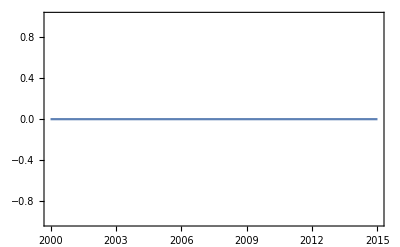

```mathematica
DateListPlot[nigerijaPodatki["Aged0To27Days"]]
```

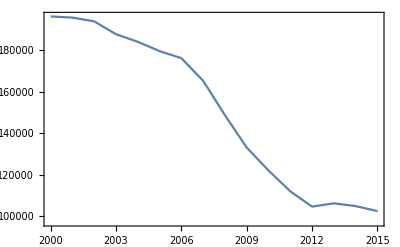

```mathematica
DateListPlot[nigerijaPodatki["Aged0To4Years"]]
```